{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{SSSSS→InterpolatingFunction[…],MMMMM→InterpolatingFunction[…]}}

{{SSSSSS→InterpolatingFunction[…],MMMMMM→InterpolatingFunction[…]}}

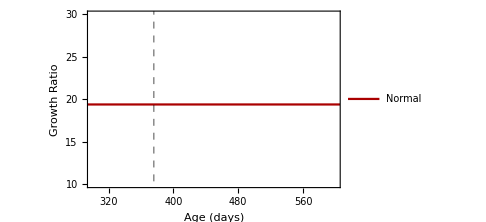

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;d=0.05;m=1000;
s1=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))* (v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==112.6,M[0]==2139.4},{S,M},{x,0,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
s5=NDSolve[{SSSSS'[x]==(2 *(P0+P1/(1+MMMMM[x]/m))-1)* (v0+v1/(1+MMMMM[x]/m))*SSSSS[x],MMMMM'[x]==2 *(1-P0-P1/(1+MMMMM[x]/m))* (v0+v1/(1+MMMMM[x]/m))* SSSSS[x]-d*MMMMM[x],SSSSS[376]==0.9*274.974,MMMMM[376]==0.8*5333.33},{SSSSS,MMMMM},{x,376,900}]
s6=NDSolve[{SSSSSS'[x]==(2 *(P0+P1/(1+MMMMMM[x]/m))-1)* (v0+v1/(1+MMMMMM[x]/m))*SSSSSS[x],MMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMM[x]/m))* (v0+v1/(1+MMMMMM[x]/m))* SSSSSS[x]-d*MMMMMM[x],SSSSSS[376]==0.8*274.974,MMMMMM[376]==0.9*5333.33},{SSSSSS,MMMMMM},{x,376,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
p1=Plot[Evaluate[(M[x]/.s1)/(S[x]/.s1)],{x,0,900},PlotRange->{{300,600},{10,30}},PlotStyle->Darker[Red],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],GridLines->{{376},{}},GridLinesStyle->Directive[Black,Dashed],PlotLegends->Placed[{"Normal"},{0.65,0.65}]]
p5=Plot[Evaluate[(MMMMM[x]/.s5)/(SSSSS[x]/.s5)],{x,376,900},PlotRange->{{376,700},{0,48}},PlotStyle->Darker[Blue],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"10% Stem & 20% Muscle Loss"},{0.65,0.85}]];
p6=Plot[Evaluate[(MMMMMM[x]/.s6)/(SSSSSS[x]/.s6)],{x,376,900},PlotRange->{{376,700},{0,48}},PlotStyle->Darker[Green],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"20% Stem & 10% Muscle Loss"},{0.65,0.75}]];
```

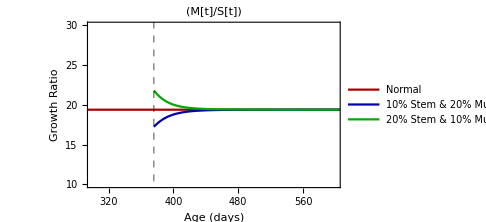

```mathematica
fig1=Show[p1,p5,p6,PlotLabel->"(M[t]/S[t])",LabelStyle->Directive[(*Bold,*)Black,13]]
```

{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{SSSSS→InterpolatingFunction[…],MMMMM→InterpolatingFunction[…]}}

{{SSSSSS→InterpolatingFunction[…],MMMMMM→InterpolatingFunction[…]}}

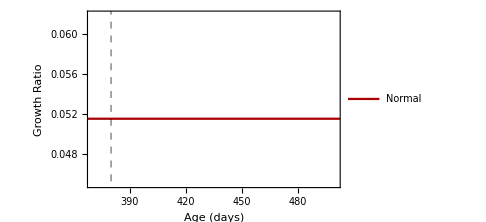

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;d=0.05;
s1=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))* (v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==112.6,M[0]==2139.4},{S,M},{x,0,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
s5=NDSolve[{SSSSS'[x]==(2 *(P0+P1/(1+MMMMM[x]/m))-1)* (v0+v1/(1+MMMMM[x]/m))*SSSSS[x],MMMMM'[x]==2 *(1-P0-P1/(1+MMMMM[x]/m))* (v0+v1/(1+MMMMM[x]/m))* SSSSS[x]-d*MMMMM[x],SSSSS[380]==0.9*1099.9,MMMMM[380]==0.8*21333.5},{SSSSS,MMMMM},{x,380,900}]
s6=NDSolve[{SSSSSS'[x]==(2 *(P0+P1/(1+MMMMMM[x]/m))-1)* (v0+v1/(1+MMMMMM[x]/m))*SSSSSS[x],MMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMM[x]/m))* (v0+v1/(1+MMMMMM[x]/m))* SSSSSS[x]-d*MMMMMM[x],SSSSSS[380]==0.8*1099.9,MMMMMM[380]==0.9*21333.5},{SSSSSS,MMMMMM},{x,380,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
p1=Plot[Evaluate[(S[x]/.s1)/(M[x]/.s1)],{x,0,900},PlotRange->{{370,500},{0.045,0.062}},PlotStyle->Darker[Red],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],GridLines->{{380},{}},GridLinesStyle->Directive[Black,Dashed],PlotLegends->Placed[{"Normal"},{0.65,0.65}]]
p5=Plot[Evaluate[(SSSSS[x]/.s5)/(MMMMM[x]/.s5)],{x,380,900},PlotRange->{{380,700},{0,10}},PlotStyle->Darker[Blue],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"10% Stem & 20% Muscle Loss"},{0.65,0.85}]];
p6=Plot[Evaluate[(SSSSSS[x]/.s6)/(MMMMMM[x]/.s6)],{x,380,900},PlotRange->{{380,700},{0,10}},PlotStyle->Darker[Green],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"20% Stem & 10% Muscle Loss"},{0.65,0.75}]];
```

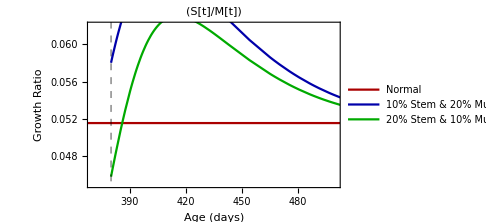

```mathematica
fig2=Show[p1,p5,p6,PlotLabel->"(S[t]/M[t])",LabelStyle->Directive[(*Bold,*)Black,13]]
```

{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{SSSSS→InterpolatingFunction[…],MMMMM→InterpolatingFunction[…]}}

{{SSSSSS→InterpolatingFunction[…],MMMMMM→InterpolatingFunction[…]}}

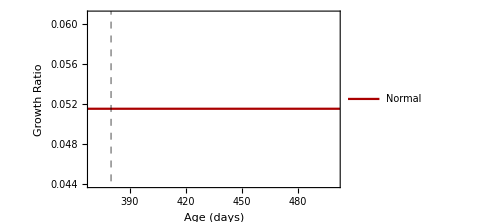

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;d=0.05;
s1=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))* (v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==112.6,M[0]==2139.4},{S,M},{x,0,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
s5=NDSolve[{SSSSS'[x]==(2 *(P0+P1/(1+MMMMM[x]/m))-1)* (v0+v1/(1+MMMMM[x]/m))*SSSSS[x],MMMMM'[x]==2 *(1-P0-P1/(1+MMMMM[x]/m))* (v0+v1/(1+MMMMM[x]/m))* SSSSS[x]-d*MMMMM[x],SSSSS[380]==0.8*1099.9,MMMMM[380]==0.7*21333.5},{SSSSS,MMMMM},{x,380,900}]
s6=NDSolve[{SSSSSS'[x]==(2 *(P0+P1/(1+MMMMMM[x]/m))-1)* (v0+v1/(1+MMMMMM[x]/m))*SSSSSS[x],MMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMM[x]/m))* (v0+v1/(1+MMMMMM[x]/m))* SSSSSS[x]-d*MMMMMM[x],SSSSSS[380]==0.7*1099.9,MMMMMM[380]==0.8*21333.5},{SSSSSS,MMMMMM},{x,380,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
p1=Plot[Evaluate[(S[x]/.s1)/(M[x]/.s1)],{x,0,900},PlotRange->{{370,500},{0.044,0.061}},PlotStyle->Darker[Red],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],GridLines->{{380},{}},GridLinesStyle->Directive[Black,Dashed],PlotLegends->Placed[{"Normal"},{0.65,0.65}]]
p5=Plot[Evaluate[(SSSSS[x]/.s5)/(MMMMM[x]/.s5)],{x,380,900},PlotRange->{{380,700},{0,10}},PlotStyle->Darker[Blue],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"20% Stem & 30% Muscle Loss"},{0.65,0.85}]];
p6=Plot[Evaluate[(SSSSSS[x]/.s6)/(MMMMMM[x]/.s6)],{x,380,900},PlotRange->{{380,700},{0,10}},PlotStyle->Darker[Green],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"30% Stem & 20% Muscle Loss"},{0.65,0.75}]];
```

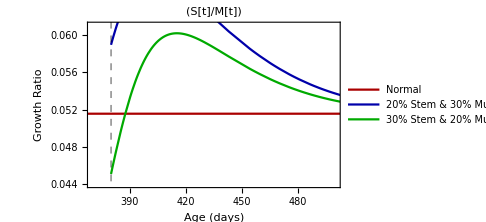

```mathematica
fig3=Show[p1,p5,p6,PlotLabel->"(S[t]/M[t])",LabelStyle->Directive[(*Bold,*)Black,13]]
```

{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{SSSSS→InterpolatingFunction[…],MMMMM→InterpolatingFunction[…]}}

{{SSSSSS→InterpolatingFunction[…],MMMMMM→InterpolatingFunction[…]}}

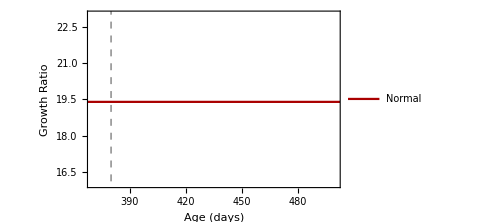

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;d=0.05;
s1=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))* (v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==112.6,M[0]==2139.4},{S,M},{x,0,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
s5=NDSolve[{SSSSS'[x]==(2 *(P0+P1/(1+MMMMM[x]/m))-1)* (v0+v1/(1+MMMMM[x]/m))*SSSSS[x],MMMMM'[x]==2 *(1-P0-P1/(1+MMMMM[x]/m))* (v0+v1/(1+MMMMM[x]/m))* SSSSS[x]-d*MMMMM[x],SSSSS[380]==0.8*1099.9,MMMMM[380]==0.7*21333.5},{SSSSS,MMMMM},{x,380,900}]
s6=NDSolve[{SSSSSS'[x]==(2 *(P0+P1/(1+MMMMMM[x]/m))-1)* (v0+v1/(1+MMMMMM[x]/m))*SSSSSS[x],MMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMM[x]/m))* (v0+v1/(1+MMMMMM[x]/m))* SSSSSS[x]-d*MMMMMM[x],SSSSSS[380]==0.7*1099.9,MMMMMM[380]==0.8*21333.5},{SSSSSS,MMMMMM},{x,380,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
p1=Plot[Evaluate[(M[x]/.s1)/(S[x]/.s1)],{x,0,900},PlotRange->{{370,500},{16,23}},PlotStyle->Darker[Red],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],GridLines->{{380},{}},GridLinesStyle->Directive[Black,Dashed],PlotLegends->Placed[{"Normal"},{0.65,0.65}]]
p5=Plot[Evaluate[(MMMMM[x]/.s5)/(SSSSS[x]/.s5)],{x,380,900},PlotRange->{{380,700},{0,48}},PlotStyle->Darker[Blue],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"20% Stem & 30% Muscle Loss"},{0.65,0.85}]];
p6=Plot[Evaluate[(MMMMMM[x]/.s6)/(SSSSSS[x]/.s6)],{x,380,900},PlotRange->{{380,700},{0,48}},PlotStyle->Darker[Green],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"30% Stem & 20% Muscle Loss"},{0.65,0.75}]];
```

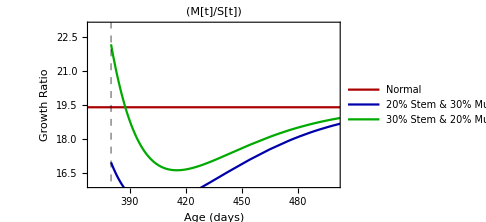

```mathematica
fig4=Show[p1,p5,p6,PlotLabel->"(M[t]/S[t])",LabelStyle->Directive[(*Bold,*)Black,13]]
```

{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{SSSSS→InterpolatingFunction[…],MMMMM→InterpolatingFunction[…]}}

{{SSSSSS→InterpolatingFunction[…],MMMMMM→InterpolatingFunction[…]}}

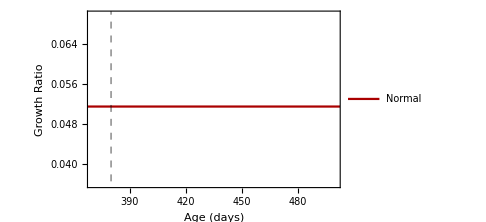

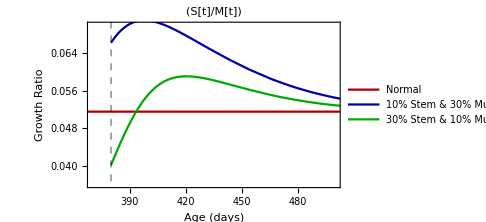

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;d=0.05;
s1=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))* (v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==112.6,M[0]==2139.4},{S,M},{x,0,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
s5=NDSolve[{SSSSS'[x]==(2 *(P0+P1/(1+MMMMM[x]/m))-1)* (v0+v1/(1+MMMMM[x]/m))*SSSSS[x],MMMMM'[x]==2 *(1-P0-P1/(1+MMMMM[x]/m))* (v0+v1/(1+MMMMM[x]/m))* SSSSS[x]-d*MMMMM[x],SSSSS[380]==0.9*1099.9,MMMMM[380]==0.7*21333.5},{SSSSS,MMMMM},{x,380,900}]
s6=NDSolve[{SSSSSS'[x]==(2 *(P0+P1/(1+MMMMMM[x]/m))-1)* (v0+v1/(1+MMMMMM[x]/m))*SSSSSS[x],MMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMM[x]/m))* (v0+v1/(1+MMMMMM[x]/m))* SSSSSS[x]-d*MMMMMM[x],SSSSSS[380]==0.7*1099.9,MMMMMM[380]==0.9*21333.5},{SSSSSS,MMMMMM},{x,380,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
p1=Plot[Evaluate[(S[x]/.s1)/(M[x]/.s1)],{x,0,900},PlotRange->{{370,500},{0.036,0.07}},PlotStyle->Darker[Red],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],GridLines->{{380},{}},GridLinesStyle->Directive[Black,Dashed],PlotLegends->Placed[{"Normal"},{0.65,0.65}]]
p5=Plot[Evaluate[(SSSSS[x]/.s5)/(MMMMM[x]/.s5)],{x,380,900},PlotRange->{{380,700},{0,10}},PlotStyle->Darker[Blue],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"10% Stem & 30% Muscle Loss"},{0.65,0.85}]];
p6=Plot[Evaluate[(SSSSSS[x]/.s6)/(MMMMMM[x]/.s6)],{x,380,900},PlotRange->{{380,700},{0,10}},PlotStyle->Darker[Green],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"30% Stem & 10% Muscle Loss"},{0.65,0.75}]];
fig5=Show[p1,p5,p6,PlotLabel->"(S[t]/M[t])",LabelStyle->Directive[(*Bold,*)Black,13]]
```

{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{SSSSS→InterpolatingFunction[…],MMMMM→InterpolatingFunction[…]}}

{{SSSSSS→InterpolatingFunction[…],MMMMMM→InterpolatingFunction[…]}}

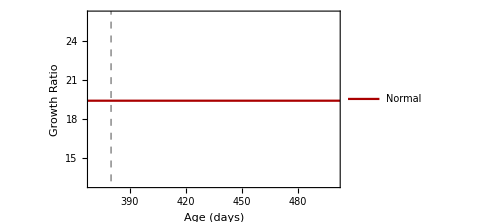

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;d=0.05;
s1=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))* (v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==112.6,M[0]==2139.4},{S,M},{x,0,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
s5=NDSolve[{SSSSS'[x]==(2 *(P0+P1/(1+MMMMM[x]/m))-1)* (v0+v1/(1+MMMMM[x]/m))*SSSSS[x],MMMMM'[x]==2 *(1-P0-P1/(1+MMMMM[x]/m))* (v0+v1/(1+MMMMM[x]/m))* SSSSS[x]-d*MMMMM[x],SSSSS[380]==0.9*1099.9,MMMMM[380]==0.7*21333.5},{SSSSS,MMMMM},{x,380,900}]
s6=NDSolve[{SSSSSS'[x]==(2 *(P0+P1/(1+MMMMMM[x]/m))-1)* (v0+v1/(1+MMMMMM[x]/m))*SSSSSS[x],MMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMM[x]/m))* (v0+v1/(1+MMMMMM[x]/m))* SSSSSS[x]-d*MMMMMM[x],SSSSSS[380]==0.7*1099.9,MMMMMM[380]==0.9*21333.5},{SSSSSS,MMMMMM},{x,380,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
p1=Plot[Evaluate[(M[x]/.s1)/(S[x]/.s1)],{x,0,900},PlotRange->{{370,500},{13,26}},PlotStyle->Darker[Red],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],GridLines->{{380},{}},GridLinesStyle->Directive[Black,Dashed],PlotLegends->Placed[{"Normal"},{0.65,0.65}]]
p5=Plot[Evaluate[(MMMMM[x]/.s5)/(SSSSS[x]/.s5)],{x,380,900},PlotRange->{{380,700},{0,48}},PlotStyle->Darker[Blue],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"10% Stem & 30% Muscle Loss"},{0.65,0.85}]];
p6=Plot[Evaluate[(MMMMMM[x]/.s6)/(SSSSSS[x]/.s6)],{x,380,900},PlotRange->{{380,700},{0,48}},PlotStyle->Darker[Green],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"30% Stem & 10% Muscle Loss"},{0.65,0.75}]];
```

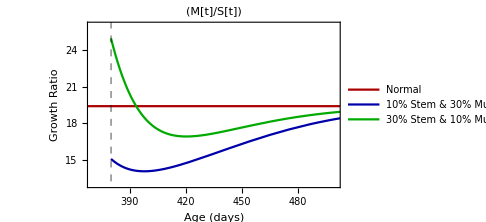

```mathematica
fig6=Show[p1,p5,p6,PlotLabel->"(M[t]/S[t])",LabelStyle->Directive[(*Bold,*)Black,13]]
```

```mathematica
Export["D:/Ex1.eps",fig1]
Export["D:/Ex2.eps",fig2]
Export["D:/Ex3.eps",fig3]
Export["D:/Ex4.eps",fig4]
Export["D:/Ex5.eps",fig5]
Export["D:/Ex6.eps",fig6]
```

D:/Ex1.eps

D:/Ex2.eps

D:/Ex3.eps

D:/Ex4.eps

D:/Ex5.eps

D:/Ex6.eps

{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{SSSSS→InterpolatingFunction[…],MMMMM→InterpolatingFunction[…]}}

{{SSSSSS→InterpolatingFunction[…],MMMMMM→InterpolatingFunction[…]}}

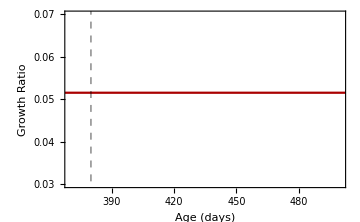

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
P0=0.479;P1=0.133;v0=0.087;v1=5.591;d=0.05;
s1=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))* (v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==112.6,M[0]==2139.4},{S,M},{x,0,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
s5=NDSolve[{SSSSS'[x]==(2 *(P0+P1/(1+MMMMM[x]/m))-1)* (v0+v1/(1+MMMMM[x]/m))*SSSSS[x],MMMMM'[x]==2 *(1-P0-P1/(1+MMMMM[x]/m))* (v0+v1/(1+MMMMM[x]/m))* SSSSS[x]-d*MMMMM[x],SSSSS[380]==0.9*1099.9,MMMMM[380]==0.8*21333.5},{SSSSS,MMMMM},{x,380,900}]
s6=NDSolve[{SSSSSS'[x]==(2 *(P0+P1/(1+MMMMMM[x]/m))-1)* (v0+v1/(1+MMMMMM[x]/m))*SSSSSS[x],MMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMM[x]/m))* (v0+v1/(1+MMMMMM[x]/m))* SSSSSS[x]-d*MMMMMM[x],SSSSSS[380]==0.9*1099.9,MMMMMM[380]==0.7*21333.5},{SSSSSS,MMMMMM},{x,380,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
p1=Plot[Evaluate[(S[x]/.s1)/(M[x]/.s1)],{x,0,900},PlotRange->{{370,500},{0.03,0.07}},PlotStyle->Darker[Red],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],GridLines->{{380},{}},GridLinesStyle->Directive[Black,Dashed](*,PlotLegends->Placed[{"Normal"},{0.45,0.1}]*)]
p5=Plot[Evaluate[(SSSSS[x]/.s5)/(MMMMM[x]/.s5)],{x,380,900},PlotRange->{{380,700},{0,10}},PlotStyle->Darker[Blue],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"10% Stem & 20% Muscle Loss"},{0.65,0.4}]];
p6=Plot[Evaluate[(SSSSSS[x]/.s6)/(MMMMMM[x]/.s6)],{x,380,900},PlotRange->{{380,700},{0,10}},PlotStyle->Darker[Green],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"10% Stem & 30% Muscle Loss"},{0.65,0.3}]];
```

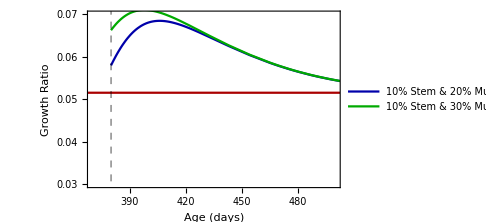

```mathematica
fi1=Show[p1,p5,p6]
```

{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{SSSSS→InterpolatingFunction[…],MMMMM→InterpolatingFunction[…]}}

{{SSSSSS→InterpolatingFunction[…],MMMMMM→InterpolatingFunction[…]}}

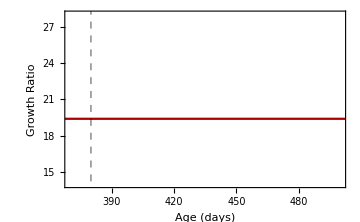

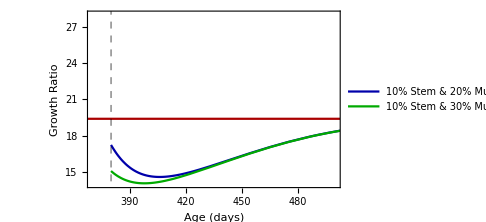

{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{SSSSS→InterpolatingFunction[…],MMMMM→InterpolatingFunction[…]}}

{{SSSSSS→InterpolatingFunction[…],MMMMMM→InterpolatingFunction[…]}}

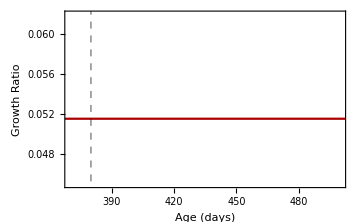

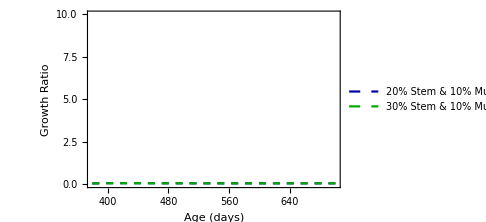

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;d=0.05;
s1=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))* (v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==112.6,M[0]==2139.4},{S,M},{x,0,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
s5=NDSolve[{SSSSS'[x]==(2 *(P0+P1/(1+MMMMM[x]/m))-1)* (v0+v1/(1+MMMMM[x]/m))*SSSSS[x],MMMMM'[x]==2 *(1-P0-P1/(1+MMMMM[x]/m))* (v0+v1/(1+MMMMM[x]/m))* SSSSS[x]-d*MMMMM[x],SSSSS[380]==0.9*1099.9,MMMMM[380]==0.8*21333.5},{SSSSS,MMMMM},{x,380,900}]
s6=NDSolve[{SSSSSS'[x]==(2 *(P0+P1/(1+MMMMMM[x]/m))-1)* (v0+v1/(1+MMMMMM[x]/m))*SSSSSS[x],MMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMM[x]/m))* (v0+v1/(1+MMMMMM[x]/m))* SSSSSS[x]-d*MMMMMM[x],SSSSSS[380]==0.9*1099.9,MMMMMM[380]==0.7*21333.5},{SSSSSS,MMMMMM},{x,380,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
p1=Plot[Evaluate[(M[x]/.s1)/(S[x]/.s1)],{x,0,900},PlotRange->{{370,500},{14,28}},PlotStyle->Darker[Red],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],GridLines->{{380},{}},GridLinesStyle->Directive[Black,Dashed](*,PlotLegends->Placed[{"Normal"},{0.65,0.9}]*)]
p5=Plot[Evaluate[(MMMMM[x]/.s5)/(SSSSS[x]/.s5)],{x,380,900},PlotRange->{{380,700},{0,400}},PlotStyle->Darker[Blue],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"10% Stem & 20% Muscle Loss"},{0.65,0.9}]];
p6=Plot[Evaluate[(MMMMMM[x]/.s6)/(SSSSSS[x]/.s6)],{x,380,900},PlotRange->{{380,700},{0,400}},PlotStyle->Darker[Green],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"10% Stem & 30% Muscle Loss"},{0.65,0.8}]];
fi2=Show[p1,p5,p6]
(*+++++++++++++++++++++++++++++++++++++++++++++*)

P0=0.479;P1=0.133;v0=0.087;v1=5.591;d=0.05;
s1=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))* (v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==112.6,M[0]==2139.4},{S,M},{x,0,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
s5=NDSolve[{SSSSS'[x]==(2 *(P0+P1/(1+MMMMM[x]/m))-1)* (v0+v1/(1+MMMMM[x]/m))*SSSSS[x],MMMMM'[x]==2 *(1-P0-P1/(1+MMMMM[x]/m))* (v0+v1/(1+MMMMM[x]/m))* SSSSS[x]-d*MMMMM[x],SSSSS[380]==0.8*1099.9,MMMMM[380]==0.9*21333.5},{SSSSS,MMMMM},{x,380,900}]
s6=NDSolve[{SSSSSS'[x]==(2 *(P0+P1/(1+MMMMMM[x]/m))-1)* (v0+v1/(1+MMMMMM[x]/m))*SSSSSS[x],MMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMM[x]/m))* (v0+v1/(1+MMMMMM[x]/m))* SSSSSS[x]-d*MMMMMM[x],SSSSSS[380]==0.7*1099.9,MMMMMM[380]==0.9*21333.5},{SSSSSS,MMMMMM},{x,380,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
p1=Plot[Evaluate[(S[x]/.s1)/(M[x]/.s1)],{x,0,900},PlotRange->{{370,500},{0.045,0.062}},PlotStyle->Darker[Red],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],GridLines->{{380},{}},GridLinesStyle->Directive[Black,Dashed](*,PlotLegends->Placed[{"Normal"},{0.65,0.65}]*)]
p5=Plot[Evaluate[(SSSSS[x]/.s5)/(MMMMM[x]/.s5)],{x,380,900},PlotRange->{{380,700},{0,10}},PlotStyle->{Darker[Blue],Dashed},(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"20% Stem & 10% Muscle Loss"},{0.62,0.2}]];
p6=Plot[Evaluate[(SSSSSS[x]/.s6)/(MMMMMM[x]/.s6)],{x,380,900},PlotRange->{{380,700},{0,10}},PlotStyle->{Darker[Green],Dashed},(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"30% Stem & 10% Muscle Loss"},{0.62,0.1}]];
fi3=Show[p5,p6]

(*+++++++++++++++++++++++++++++++++++++++++++++*)
```

{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{SSSSS→InterpolatingFunction[…],MMMMM→InterpolatingFunction[…]}}

{{SSSSSS→InterpolatingFunction[…],MMMMMM→InterpolatingFunction[…]}}

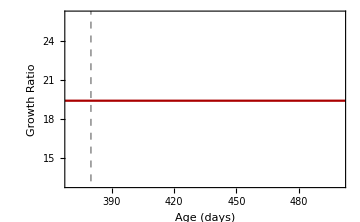

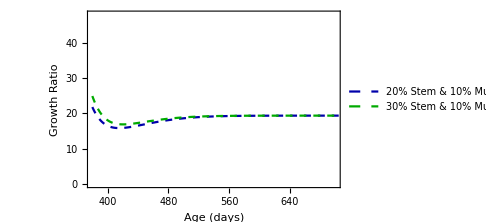

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;d=0.05;
s1=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))* (v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==112.6,M[0]==2139.4},{S,M},{x,0,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
s5=NDSolve[{SSSSS'[x]==(2 *(P0+P1/(1+MMMMM[x]/m))-1)* (v0+v1/(1+MMMMM[x]/m))*SSSSS[x],MMMMM'[x]==2 *(1-P0-P1/(1+MMMMM[x]/m))* (v0+v1/(1+MMMMM[x]/m))* SSSSS[x]-d*MMMMM[x],SSSSS[380]==0.8*1099.9,MMMMM[380]==0.9*21333.5},{SSSSS,MMMMM},{x,380,900}]
s6=NDSolve[{SSSSSS'[x]==(2 *(P0+P1/(1+MMMMMM[x]/m))-1)* (v0+v1/(1+MMMMMM[x]/m))*SSSSSS[x],MMMMMM'[x]==2 *(1-P0-P1/(1+MMMMMM[x]/m))* (v0+v1/(1+MMMMMM[x]/m))* SSSSSS[x]-d*MMMMMM[x],SSSSSS[380]==0.7*1099.9,MMMMMM[380]==0.9*21333.5},{SSSSSS,MMMMMM},{x,380,900}]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
p1=Plot[Evaluate[(M[x]/.s1)/(S[x]/.s1)],{x,0,900},PlotRange->{{370,500},{13,26}},PlotStyle->Darker[Red],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],GridLines->{{380},{}},GridLinesStyle->Directive[Black,Dashed](*PlotLegends->Placed[{"Normal"},{0.65,0.65}]*)]
p5=Plot[Evaluate[(MMMMM[x]/.s5)/(SSSSS[x]/.s5)],{x,380,900},PlotRange->{{380,700},{0,48}},PlotStyle->{Darker[Blue],Dashed},(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"20% Stem & 10% Muscle Loss"},{0.65,0.7}]];
p6=Plot[Evaluate[(MMMMMM[x]/.s6)/(SSSSSS[x]/.s6)],{x,380,900},PlotRange->{{380,700},{0,48}},PlotStyle->{Darker[Green],Dashed},(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12](*,PlotLabel->"(A)"*),LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"30% Stem & 10% Muscle Loss"},{0.65,0.6}]];
(*+++++++++++++++++++++++++++++++++++++++++++++*)
fi4=Show[p5,p6]
```

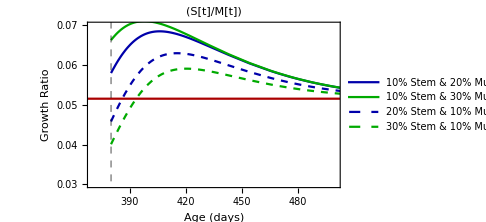

```mathematica
fs1=Show[fi1,fi3,PlotLabel->"(S[t]/M[t])",LabelStyle->Directive[(*Bold,*)Black,13]]
```

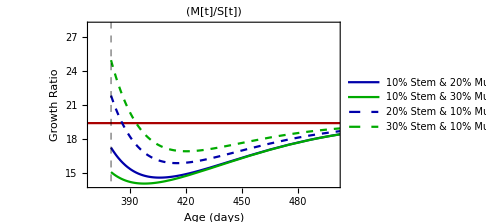

```mathematica
fs2=Show[fi2,fi4,PlotLabel->"(M[t]/S[t])",LabelStyle->Directive[(*Bold,*)Black,13]]
```

```mathematica
Export["D:/Ex7.eps",fs1]
Export["D:/Ex8.eps",fs2]
```

D:/Ex7.eps

D:/Ex8.eps